# Jan 2022

```mathematica
SetDirectory[NotebookDirectory[]];
cd=ColorData[97,"ColorList"];
```

## 0. Connectome

```mathematica
iw2 =Import["/Users/eduardoizquierdo/Github/MultifunctionalAnalysisv2/TimeSeries/1/interweightsX.dat"];
```

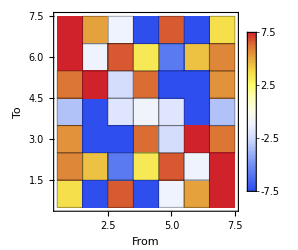

```mathematica
ListDensityPlot[iw2,InterpolationOrder->0,Mesh->All,ColorFunction->"TemperatureMap",PlotRange->{{0.5,7.5},{0.5,7.5},{-7.5,7.5}},ClippingStyle->{Darker[Blue],Darker[Red]},Frame->True,FrameLabel->{"From","To"},ImageSize->250,PlotLegends->Automatic]
Export["f_weights.eps",%];
```

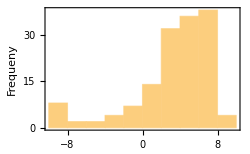

```mathematica
Histogram[Flatten[iw2],PlotRange->All,Frame->True,FrameLabel->{"Weight strength","Frequeny"},ImageSize->250]
Export["f_weightshist.eps",%];
```

## 1a. Neural Activity

```mathematica
dir2="TimeSeries/1/";
```

### Task Circle Categorization

#### Avoid

```mathematica
ba1=Import[StringJoin[dir2,"B_avoid_n1.dat"]];
ba2=Import[StringJoin[dir2,"B_avoid_n2.dat"]];
ba3=Import[StringJoin[dir2,"B_avoid_n3.dat"]];
ba4=Import[StringJoin[dir2,"B_avoid_n4.dat"]];
ba5=Import[StringJoin[dir2,"B_avoid_n5.dat"]];
ba6=Import[StringJoin[dir2,"B_avoid_n6.dat"]];
ba7=Import[StringJoin[dir2,"B_avoid_n7.dat"]];
```

#### Approach

```mathematica
bc1=Import[StringJoin[dir2,"B_approach_n1.dat"]];
bc2=Import[StringJoin[dir2,"B_approach_n2.dat"]];
bc3=Import[StringJoin[dir2,"B_approach_n3.dat"]];
bc4=Import[StringJoin[dir2,"B_approach_n4.dat"]];
bc5=Import[StringJoin[dir2,"B_approach_n5.dat"]];
bc6=Import[StringJoin[dir2,"B_approach_n6.dat"]];
bc7=Import[StringJoin[dir2,"B_approach_n7.dat"]];
```

```mathematica
(*GraphicsColumn[
{
Show[{
ListLinePlot[bc1,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba1,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc2,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba2,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc3,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba3,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc4,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba4,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc5,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba5,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc6,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba6,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc7,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba7,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
Export["ObjectRecog.eps",%]*)
```

```mathematica
b1=Flatten[{bc1,ba1}];
b2=Flatten[{bc2,ba2}];
b3=Flatten[{bc3,ba3}];
b4=Flatten[{bc4,ba4}];
b5=Flatten[{bc5,ba5}];
b6=Flatten[{bc6,ba6}];
b7=Flatten[{bc7,ba7}];
```

```mathematica
b = {b1,b2,b3,b4,b5,b6,b7};
```

```mathematica
(*step = 1000;
GraphicsGrid[Table[ListPlot[Take[Transpose[{b[[x]],b[[y]]}],{1,Length[b1],step}],PlotRange->{{-0.01,1.01},{-0.01,1.01}},PlotMarkers->Automatic,FrameTicks->False,Frame->True,Axes->False,AspectRatio->1,ImageSize->150] ,{x,1,7},{y,1,7}]]*)
```

```mathematica
corr = Table[{x,y,Correlation[b[[x]],b[[y]]]},{x,1,7},{y,1,7}]
```

{{{1,1,1.},{1,2,-0.219507},{1,3,0.406588},{1,4,-0.348253},{1,5,-0.548003},{1,6,0.565573},{1,7,0.328199}},{{2,1,-0.219507},{2,2,1.},{2,3,0.0580732},{2,4,-0.220955},{2,5,0.783477},{2,6,0.364635},{2,7,0.552524}},{{3,1,0.406588},{3,2,0.0580732},{3,3,1.},{3,4,-0.0335624},{3,5,-0.176508},{3,6,0.705282},{3,7,-0.161076}},{{4,1,-0.348253},{4,2,-0.220955},{4,3,-0.0335624},{4,4,1.},{4,5,0.158117},{4,6,-0.484278},{4,7,-0.171608}},{{5,1,-0.548003},{5,2,0.783477},{5,3,-0.176508},{5,4,0.158117},{5,5,1.},{5,6,-0.205423},{5,7,0.453047}},{{6,1,0.565573},{6,2,0.364635},{6,3,0.705282},{6,4,-0.484278},{6,5,-0.205423},{6,6,1.},{6,7,0.0872549}},{{7,1,0.328199},{7,2,0.552524},{7,3,-0.161076},{7,4,-0.171608},{7,5,0.453047},{7,6,0.0872549},{7,7,1.}}}

```mathematica
Flatten[corr,1]
```

{{1,1,1.},{1,2,-0.219507},{1,3,0.406588},{1,4,-0.348253},{1,5,-0.548003},{1,6,0.565573},{1,7,0.328199},{2,1,-0.219507},{2,2,1.},{2,3,0.0580732},{2,4,-0.220955},{2,5,0.783477},{2,6,0.364635},{2,7,0.552524},{3,1,0.406588},{3,2,0.0580732},{3,3,1.},{3,4,-0.0335624},{3,5,-0.176508},{3,6,0.705282},{3,7,-0.161076},{4,1,-0.348253},{4,2,-0.220955},{4,3,-0.0335624},{4,4,1.},{4,5,0.158117},{4,6,-0.484278},{4,7,-0.171608},{5,1,-0.548003},{5,2,0.783477},{5,3,-0.176508},{5,4,0.158117},{5,5,1.},{5,6,-0.205423},{5,7,0.453047},{6,1,0.565573},{6,2,0.364635},{6,3,0.705282},{6,4,-0.484278},{6,5,-0.205423},{6,6,1.},{6,7,0.0872549},{7,1,0.328199},{7,2,0.552524},{7,3,-0.161076},{7,4,-0.171608},{7,5,0.453047},{7,6,0.0872549},{7,7,1.}}

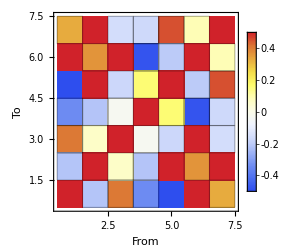

```mathematica
ListDensityPlot[Flatten[corr,1],InterpolationOrder->0,Mesh->All,ColorFunction->"TemperatureMap",PlotRange->{{0.5,7.5},{0.5,7.5},{-0.5,0.5}},ClippingStyle->{Darker[Blue],Darker[Red]},Frame->True,FrameLabel->{"From","To"},ImageSize->250,PlotLegends->Automatic]
Export["bbb_1.eps",%];
```

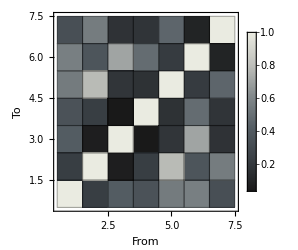

```mathematica
ListDensityPlot[Abs[Flatten[corr,1]],InterpolationOrder->0,Mesh->All,ColorFunction->"GrayTones",PlotRange->{{0.5,7.5},{0.5,7.5},{0,1.0}},ClippingStyle->{Darker[Blue],Darker[Red]},Frame->True,FrameLabel->{"From","To"},ImageSize->250,PlotLegends->Automatic]
Export["bbb_2.pdf",%];
```

```mathematica
corr = Abs[Table[{x,y,Correlation[b[[x]],b[[y]]]},{x,1,7},{y,x+1,7}]]
```

{{{1,2,0.219507},{1,3,0.406588},{1,4,0.348253},{1,5,0.548003},{1,6,0.565573},{1,7,0.328199}},{{2,3,0.0580732},{2,4,0.220955},{2,5,0.783477},{2,6,0.364635},{2,7,0.552524}},{{3,4,0.0335624},{3,5,0.176508},{3,6,0.705282},{3,7,0.161076}},{{4,5,0.158117},{4,6,0.484278},{4,7,0.171608}},{{5,6,0.205423},{5,7,0.453047}},{{6,7,0.0872549}},{}}

```mathematica
Sort[Flatten[corr,1],#1[[3]]<#2[[3]]&]
```

{{3,4,0.0335624},{2,3,0.0580732},{6,7,0.0872549},{4,5,0.158117},{3,7,0.161076},{4,7,0.171608},{3,5,0.176508},{5,6,0.205423},{1,2,0.219507},{2,4,0.220955},{1,7,0.328199},{1,4,0.348253},{2,6,0.364635},{1,3,0.406588},{5,7,0.453047},{4,6,0.484278},{1,5,0.548003},{2,7,0.552524},{1,6,0.565573},{3,6,0.705282},{2,5,0.783477}}

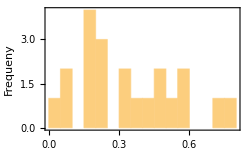

```mathematica
Histogram[Abs[Transpose[Flatten[corr,1]][[3]]],20,PlotRange->All,Frame->True,FrameLabel->{"Absolute correlation","Frequeny"},ImageSize->250]
Export["bbb_3.eps",%];
```

```mathematica
corr
```

{{{1,2,0.219507},{1,3,0.406588},{1,4,0.348253},{1,5,0.548003},{1,6,0.565573},{1,7,0.328199}},{{2,3,0.0580732},{2,4,0.220955},{2,5,0.783477},{2,6,0.364635},{2,7,0.552524}},{{3,4,0.0335624},{3,5,0.176508},{3,6,0.705282},{3,7,0.161076}},{{4,5,0.158117},{4,6,0.484278},{4,7,0.171608}},{{5,6,0.205423},{5,7,0.453047}},{{6,7,0.0872549}},{}}

```mathematica
Abs[Transpose[Flatten[corr,1]][[3]]]
```

{0.219507,0.406588,0.348253,0.548003,0.565573,0.328199,0.0580732,0.220955,0.783477,0.364635,0.552524,0.0335624,0.176508,0.705282,0.161076,0.158117,0.484278,0.171608,0.205423,0.453047,0.0872549}

```mathematica
re={{0.21950717930085734,0.932095},{0.4065879895776363,0.874266},{0.3482531011338387,0.99959},{0.5480029977005361,0.56901},{0.5655727344990144,0.94025},{0.32819860888644087,0.939835},{0.058073215013106645,0.999746},{0.22095468956143188,0.999908},{0.7834769698325731,0.995894},{0.3646349505605406,0.999927},{0.552523566880406,0.956437},{0.03356240151145162,0.77975},{0.17650769725735108,0.999198},{0.7052815734120574,0.978438},{0.1610758786090956,0.747138},{0.1581172772394143,0.819681},{0.4842776743285537,0.99991},{0.17160832650742572,0.999062},{0.20542329111662014,0.999668},{0.4530474781015212,0.834526},{0.08725494159386067,0.533549}};
```

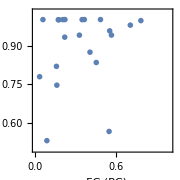

```mathematica
ListPlot[re,PlotRange->{{0,1},{0.5,1.03}},AspectRatio->1,Frame->True,FrameLabel->{"nFC (PC)","Two way info lesions"},ImageSize->Small,PlotMarkers->"OpenMarkers"]
Export["relation.eps",%];
```

## Two Way Lesions

```mathematica
dir2 ="SysLesions/1/";
```

```mathematica
B=Import[StringJoin[dir2,"Bx.dat"]];
```

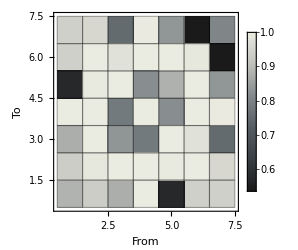

```mathematica
ListDensityPlot[B,InterpolationOrder->0,Mesh->All,ColorFunction->"GrayTones",PlotRange->{{0.5,7.5},{0.5,7.5},All},ClippingStyle->{Darker[Blue],Darker[Red]},Frame->True,FrameLabel->{"From","To"},ImageSize->250,PlotLegends->Automatic]
Export["bbb_1.eps",%];
```

```mathematica
B=Import[StringJoin[dir2,"Bxx.dat"]];
```

```mathematica
B
```

{{2,1,0.932095},{3,1,0.874266},{3,2,0.999746},{4,1,0.99959},{4,2,0.999908},{4,3,0.77975},{5,1,0.56901},{5,2,0.995894},{5,3,0.999198},{5,4,0.819681},{6,1,0.94025},{6,2,0.999927},{6,3,0.978438},{6,4,0.99991},{6,5,0.999668},{7,1,0.939835},{7,2,0.956437},{7,3,0.747138},{7,4,0.999062},{7,5,0.834526},{7,6,0.533549}}

```mathematica
Sort[B,#1[[3]]<#2[[3]]&]
```

{{7,6,0.533549},{5,1,0.56901},{7,3,0.747138},{4,3,0.77975},{5,4,0.819681},{7,5,0.834526},{3,1,0.874266},{2,1,0.932095},{7,1,0.939835},{6,1,0.94025},{7,2,0.956437},{6,3,0.978438},{5,2,0.995894},{7,4,0.999062},{5,3,0.999198},{4,1,0.99959},{6,5,0.999668},{3,2,0.999746},{4,2,0.999908},{6,4,0.99991},{6,2,0.999927}}

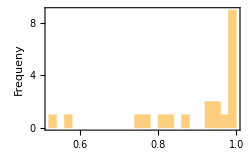

```mathematica
Histogram[Transpose[B][[3]],15,PlotRange->All,Frame->True,FrameLabel->{"Lesion impact on Performance","Frequeny"},ImageSize->250]
Export["bbb_3.eps",%];
```

## One Way Lesions

```mathematica
dir2 ="SysLesions/1/";
```

```mathematica
A=Import[StringJoin[dir2,"oneway_sysedge_iw_A.dat"]];
B=Import[StringJoin[dir2,"oneway_sysedge_iw_B.dat"]];
```

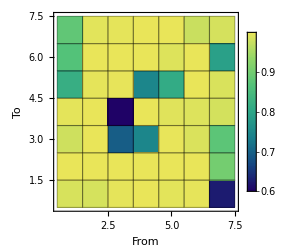

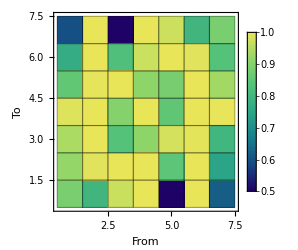

```mathematica
ListDensityPlot[A,InterpolationOrder->0,Mesh->All,PlotRange->{{0.5,7.5},{0.5,7.5},{0.5,1.0}},ColorFunction->"BlueGreenYellow",Frame->True,FrameLabel->{"From","To"},ImageSize->250,PlotLegends->Automatic]
ListDensityPlot[B,InterpolationOrder->0,Mesh->All,PlotRange->{{0.5,7.5},{0.5,7.5},{0.5,1.0}},ColorFunction->"BlueGreenYellow",Frame->True,FrameLabel->{"From","To"},ImageSize->250,PlotLegends->Automatic]
```